```mathematica
Show[{
Plot3D[y^2-x^2,{x,-10,10},{y,-10,10},PlotRange->{-20,20},ClippingStyle->None,Boxed->False,Axes->None,PlotStyle->Opacity[0.25]],
Graphics3D[{
Red,PointSize[0.025],Point[{0,0,0}]
}]
}]
```

-Graphics3D-

```mathematica
?Epilog
```

Epilog is an option for graphics functions that gives a list of graphics primitives to be rendered after the main part of the graphics is rendered.

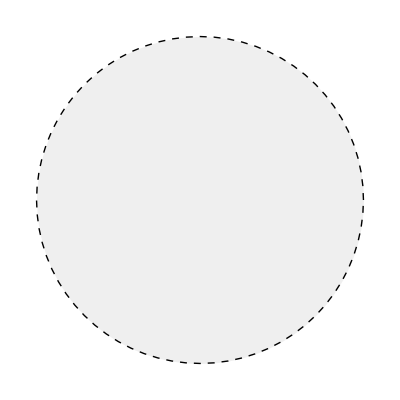

```mathematica
Graphics[{
{Dashed,Circle[]},
{Opacity[0.0625],Disk[]}
}]
```

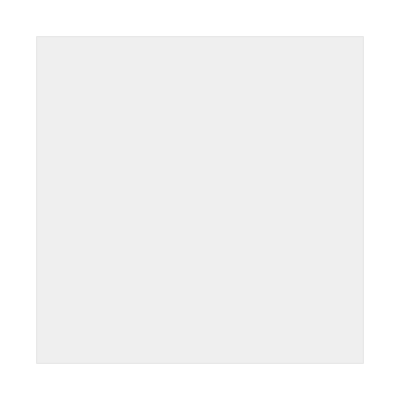

```mathematica
Graphics[{
{Opacity[0.0625],EdgeForm[{Black}],Rectangle[{0,0},{2,2}]}
}]
```

```mathematica
Graphics[{
{InfiniteLine[{{0,0},{2,1}}]},
{Opacity[0.0625],HalfPlane[{{0,0},{2,1}},{0,-1}]}
}]
```

-Graphics-

```mathematica
Graphics[{
{Dashed,InfiniteLine[{{0,0},{-1,-3}}]},
{Opacity[0.0625],HalfPlane[{{0,0},{-1,-3}},{0,-1}]}
}]
```

-Graphics-

```mathematica
?Square
```

Square[x] displays as □x.

```mathematica
?Polygon
```

Polygon[{p_1,…,p_n}] represents a filled polygon with points p_i.
Polygon[{{p_11,…},{p_21,…},…}] represents a collection of polygons.

```mathematica
?EdgeForm
```

EdgeForm[g] is a graphics directive that specifies that edges of polygons and other filled graphics objects are to be drawn using the graphics directive or list of directives g.